# Studying deformation near soft singularity in e^+e^-→γ^*→d d̄

## Resources

```mathematica
RustBindingsPath="/Users/valentin/Documents/MG5/old_madnklk/PLUGIN/pynloop/Mathematica";
AlphaLoopPath="/Users/valentin/Documents/MG5/old_madnklk/PLUGIN/pynloop";
```

```mathematica
Get[RustBindingsPath<>"/"<>"RustFromMathematica.m"]
```

Package for accessing alphaLoop implementation in Rust.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Make sure a stat folder exists in the local directory:

```mathematica
If[Not[DirectoryQ[NotebookDirectory[]<>"/stats"]],CreateDirectory[NotebookDirectory[]<>"stats"]];
```

Generic expression of ellipsoids, we will consider the triangle loop graph in k-space (i.e. to the left of the cutkosky cut, so cut_ID=2), with the following momentum routing:

-Graphics-

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_]:=Flatten[Table[{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0},{i, 1,N},{j,i+1,N}]]
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
RFM$KillAllHooks[];
DeformUVDampenAfterLambda10Hook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/deform_UV_dampen_after_constant_lambda10.yaml",
DEBUG->False
];

NoDeformationHook=RFM$GetLTDHook[AlphaLoopPath<>"/LTD/squared_amplitudes/ee_to_dd_2l_doubletriangle.yaml",
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/NoDeformation.yaml",
DEBUG->False
];
{RFM$CheckHookStatus[DeformUVDampenAfterLambda10Hook],RFM$CheckHookStatus[NoDeformationHook]}
```

{True,True}

Useful 3D euclidean norm

```mathematica
VDot[k_]:=k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2
```

## Deformation study

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_,OptionsPattern[{Contour->False}]]:=Flatten[Table[
If[OptionValue[Contour],
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]==0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]==0},
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0}
],{i, 1,N},{j,i+1,N}]]
```

```mathematica
TriangleP1={0,0,0};
TriangleP10=2.0;
TriangleP2={N[1/Sqrt[2],16],N[1/Sqrt[2],16],0};
TriangleP20=Sqrt[VDot[TriangleP2]];
```

Apply rescaling

```mathematica
GetRescaling[l_]:=Block[{RescalingSolutions},
RescalingSolutions=RFM$GetRescaling[DeformUVDampenAfterLambda10Hook,2,{{0,0,0},l}];
If[RescalingSolutions["tSolutions"]⟦1⟧>0,
{RescalingSolutions["tSolutions"]⟦1⟧,RescalingSolutions["tJacobians"]⟦1⟧},
{RescalingSolutions["tSolutions"]⟦2⟧,RescalingSolutions["tJacobians"]⟦2⟧}
]
]
```

```mathematica
RescalingFactor=GetRescaling[TriangleP2]⟦1⟧;
RescalingJacobian=GetRescaling[TriangleP2]⟦2⟧;
TriangleP2*= RescalingFactor;
TriangleP20*=RescalingFactor;
SoftPoint=TriangleP2*RescalingFactor;
```

Now that the kinematics is set, generate all ellipsoids

```mathematica
AllTriangleEllipsoids=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->False];
AllTriangleEllipsoidsContour=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->True];
```

And define functions accessing the deformation for the particular case of interest

```mathematica
GetDeformationVector[kx_?NumberQ,ky_?NumberQ,kz_?NumberQ]:=Block[{DeformedMomenta},
DeformedMomenta=RFM$GetCrossSectionDeformation[DeformUVDampenAfterLambda10Hook,2,{{kx,ky,kz},TriangleP2/RescalingFactor},DEBUG->False];
Im[-DeformedMomenta["DeformedMomenta"]]
]
```

```mathematica
GetDeformationVectorXY[kx_?NumericQ,ky_?NumberQ]:=Block[
{Kappas},
Kappas=GetDeformationVector[kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor];
{Kappas⟦1⟧⟦2⟧,Kappas⟦1⟧⟦3⟧}
]
```

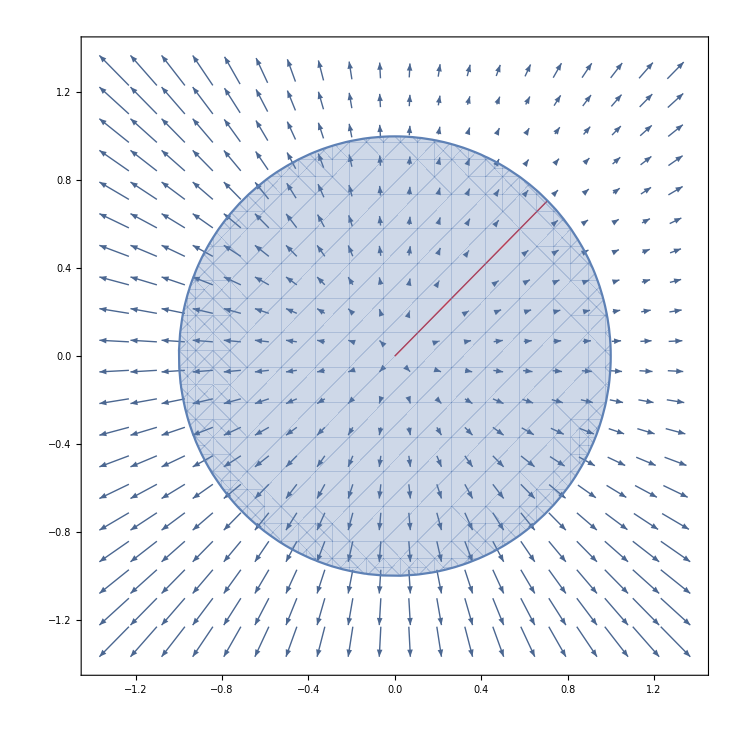

```mathematica
ZoomedOutDeformation=Show[
VectorPlot[GetDeformationVectorXY[kx,ky],{kx,-1.3,1.3},{ky,-1.3,1.3},VectorPoints->20],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
RegionPlot[
AllTriangleEllipsoids[[3]],{kx,-1,2},{ky,-1,2},
Axes->False,
Frame->True,
ImagePadding->1
]
]
```

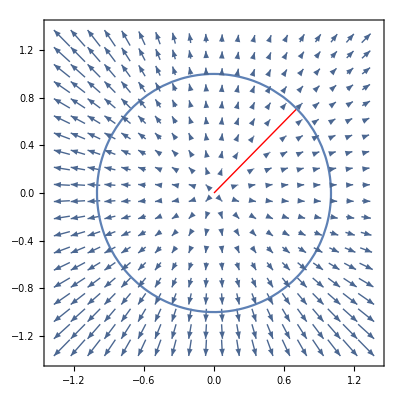

```mathematica
ZoomedOutDeformationContour=Show[
VectorPlot[GetDeformationVectorXY[kx,ky],{kx,-1.3,1.3},{ky,-1.3,1.3},VectorPoints->20],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],{kx,-1,2},{ky,-1,2},
Axes->False,
Frame->True,
ImagePadding->1
]
]
```

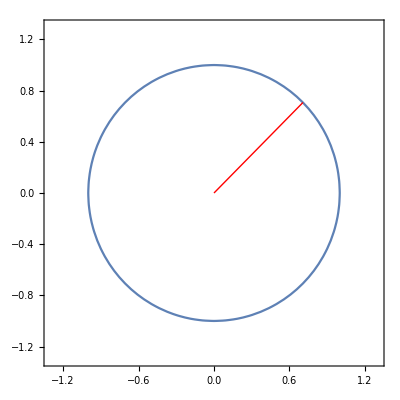

```mathematica
ZoomedOutNoDeformationContour=Show[
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],{kx,-1.3,1.3},{ky,-1.3,1.3},
Axes->False,
Frame->True,
ImagePadding->1
],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}]
]
```

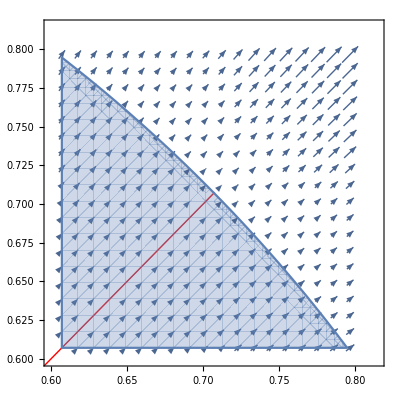

```mathematica
ZoomedInDeformation=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
VectorPlot[GetDeformationVectorXY[kx,ky],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
VectorPoints->20],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
RegionPlot[
AllTriangleEllipsoids[[3]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
]
]
]
```

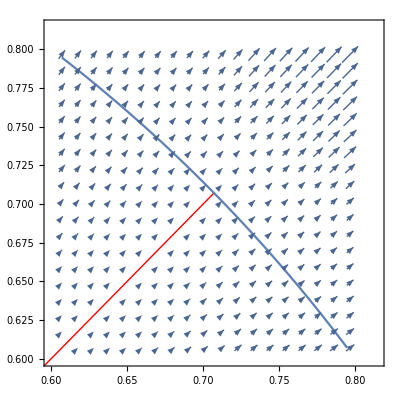

```mathematica
ZoomedInDeformationContour=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
VectorPlot[GetDeformationVectorXY[kx,ky],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
VectorPoints->20],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}],
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
]
]
]
```

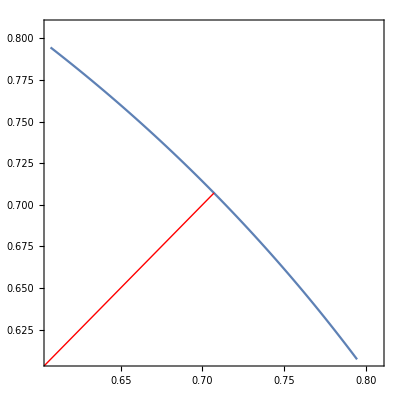

```mathematica
ZoomedInNoDeformationContour=Block[{ZoomDelta},
ZoomDelta=0.1;
Show[
ContourPlot[
Evaluate[AllTriangleEllipsoidsContour[[3]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta},
Axes->False,
Frame->True,
ImagePadding->1
],
Graphics[{Thick,Red,Line[{{0,0},SoftPoint⟦;;2⟧}]}]
]
]
```

```mathematica
EvaluateCutXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[DEBUG->False]]:=Block[
{},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
RFM$EvaluateCut[hook,2,RescalingFactor,RescalingJacobian,{{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},TriangleP2/RescalingFactor},DEBUG->False,f128->False]
]
```

```mathematica
MyReDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateCutXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyImDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Im[EvaluateCutXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

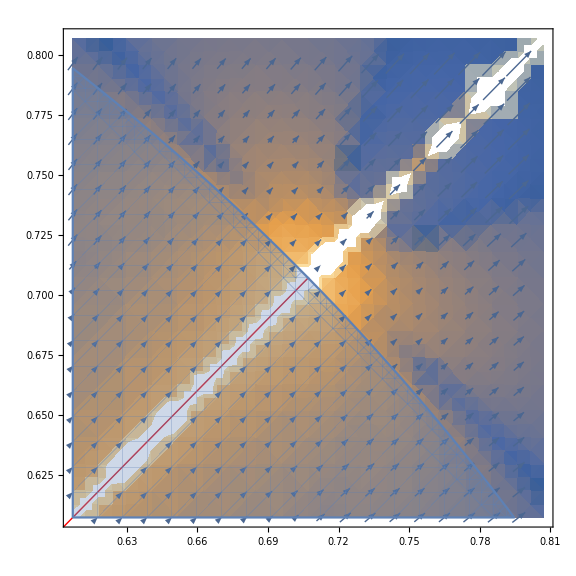
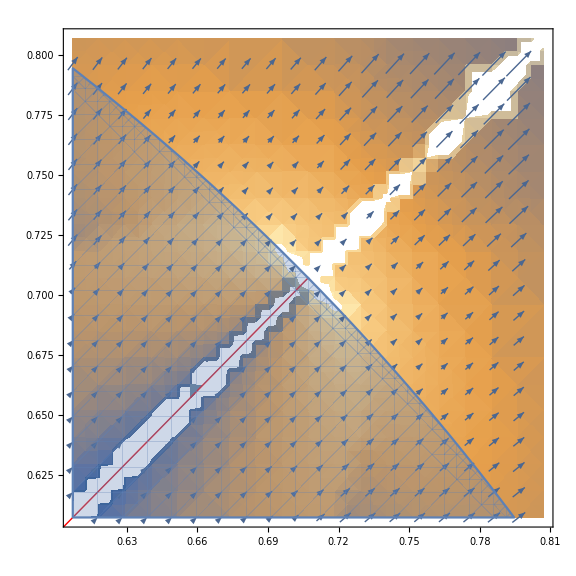
-Graphics-Im[(LTD^2@cut2] | -Graphics-Re[LTD^2@cut2]

```mathematica
Grid[{{
Labeled[Show[MyReDensityPlot,ZoomedInDeformation,ImageSize->Large],"Im[(LTD^2@cut2]"],
Labeled[Show[MyImDensityPlot,ZoomedInDeformation,ImageSize->Large],"Re[LTD^2@cut2]"]
}}]
```

```mathematica
EvaluateFullXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[DEBUG->False]]:=Block[
{invParametrizeK,invParametrizeL},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
invParametrizeK=RFM$InvParameterize[hook,0,2,{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invParametrizeL=RFM$InvParameterize[hook,1,2,TriangleP2/RescalingFactor,DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]]
]
```

```mathematica
MyFullEvalReDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

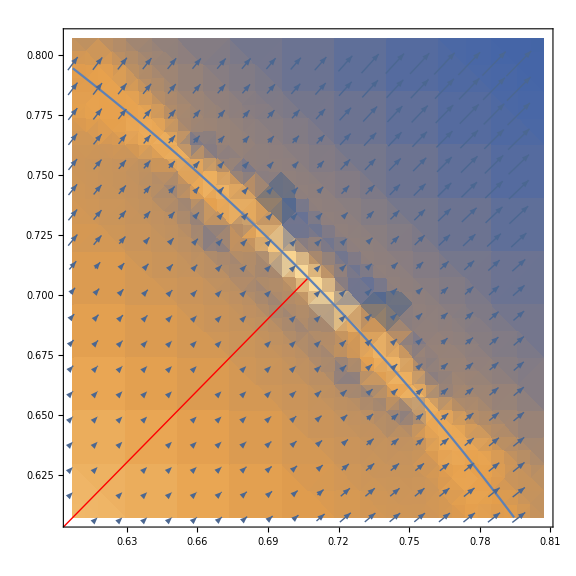
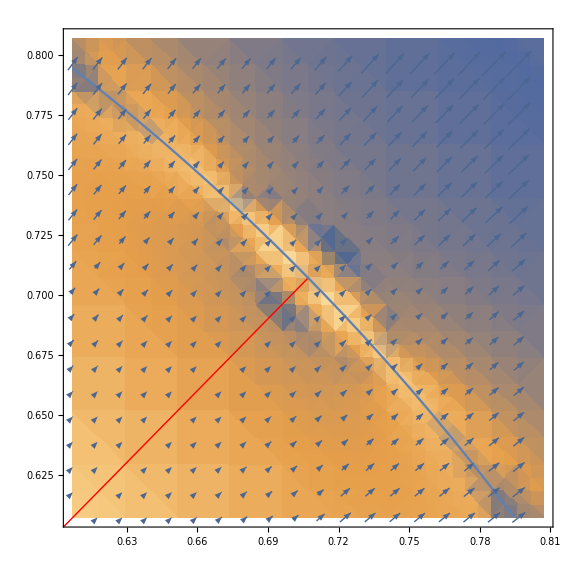
-Graphics-Im[LTD^2@full] | -Graphics-Re[LTD^2@full]

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlot,ZoomedInDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

```mathematica
MyFullEvalReNoDeformationDensityPlot=Block[
{ZoomDelta},
ZoomDelta=0.1;
DensityPlot[Log[Abs[Re[EvaluateFullXY[NoDeformationHook,kx,ky,DEBUG->False]]]],
{kx,SoftPoint⟦1⟧-ZoomDelta,SoftPoint⟦1⟧+ZoomDelta},
{ky,SoftPoint⟦2⟧-ZoomDelta,SoftPoint⟦2⟧+ZoomDelta}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

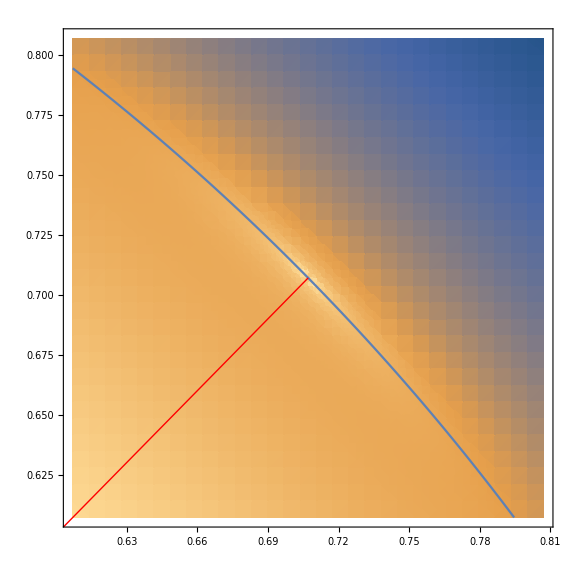
-Graphics-Re[LTD^2@full] with no deformation

```mathematica
Labeled[Show[MyFullEvalReNoDeformationDensityPlot,ZoomedInNoDeformationContour,ImageSize->Large],"Re[LTD^2@full] with no deformation"]
```

### Zoomed-out plots

```mathematica
MyFullEvalReDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Re[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
MyFullEvalImDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Im[EvaluateFullXY[DeformUVDampenAfterLambda10Hook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
Grid[{{
Labeled[Show[MyFullEvalReDensityPlotZoomedOut,ZoomedOutDeformationContour,ImageSize->Large],"Im[LTD^2@full]"],
Labeled[Show[MyFullEvalImDensityPlotZoomedOut,ZoomedOutDeformationContour,ImageSize->Large],"Re[LTD^2@full]"]
}}]
```

```mathematica
MyFullEvalReNoDeformationDensityPlotZoomedOut=Block[
{},
DensityPlot[Log[Abs[Re[EvaluateFullXY[NoDeformationHook,kx,ky,DEBUG->False]]]],
{kx,-1.3,1.3},
{ky,-1.3,1.3}, 
PlotPoints->10,Axes->False,
Frame->True,
ImagePadding->1]
];
```

```mathematica
Labeled[Show[MyFullEvalReNoDeformationDensityPlotZoomedOut,ZoomedOutNoDeformationContour,ImageSize->Large],"Re[LTD^2@full] with no deformation"]
```